```mathematica
Mod[{2,2^2,2^3,2^4,2^5,2^6,2^7,2^8, 2^9, 2^10, 2^11, 2^12, 2^13, 2^14, 2^15, 2^16},11]
```

{2,4,8,5,10,9,7,3,6,1,2,4,8,5,10,9}

## Ploting a circle Given a specific clock (e.g. 7) what happens when we modulate multiples of other clocks (cycles) into it (e.g. multipleds of 2)

```mathematica
mod2 = PolarTicks[
```

```mathematica
radius = 4
```

4

```mathematica
baseModulus=7
```

7

```mathematica
cycleModulus=3
```

3

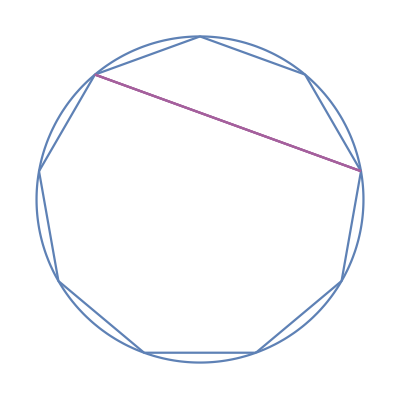

```mathematica
Show[
(*the circle*)PolarPlot[radius, {t,0,2Pi}, Axes -> False], 
(*the base modulus*)ListLinePlot[Join[CirclePoints[radius,baseModulus], Partition[First[CirclePoints[radius,baseModulus]], 2]]],
(*the cycle modulus*)ListLinePlot[Map[CirclePoints[radius,baseModulus][[#]]&, Map[ Mod[#*cycleModulus,baseModulus]&,Table[i,{i,1,baseModulus}]]]]
]
```

```mathematica
{
Slider[Dynamic[baseModulus],{0,10,1}],
Slider[Dynamic[cycleModulus], {0,100,1}],
Dynamic[Show[
(*the circle*)PolarPlot[radius, {t,0,2Pi}, Axes -> False], 
(*the base modulus*)ListLinePlot[Join[CirclePoints[radius,baseModulus], Partition[First[CirclePoints[radius,baseModulus]], 2]]],
(*the cycle modulus*)ListLinePlot[Map[CirclePoints[radius,baseModulus][[#]]&, Map[ Mod[#*cycleModulus,baseModulus]&,Table[i,{i,1,7}]]]]
]
]
}
```

{,,}

```mathematica
Animate[
Show[
(*the circle*)PolarPlot[radius, {t,0,2Pi}, Axes -> False], 
(*the base modulus*)ListLinePlot[Join[CirclePoints[radius,baseModulus], Partition[First[CirclePoints[radius,baseModulus]], 2]]],
(*the cycle modulus*)ListLinePlot[Map[CirclePoints[radius,baseModulus][[#]]&, Map[ Mod[#*cycleModulus,baseModulus]&,Table[i,{i,1,300}]]]]
],
{baseModulus, 1,10,1},
{cycleModulus, 1,100,1}
]
```